Resources
https://mathematica.stackexchange.com/questions/268990/how-can-i-efficiently-calculate-exact-probability-distributions-for-dd-dice-lik

https://mathematica.stackexchange.com/questions/164151/combine-two-lists-with-all-possible-combinations

https://rpg.stackexchange.com/questions/15971/is-it-possible-to-produce-a-bowl-shaped-probability-curve-with-dice-rolls

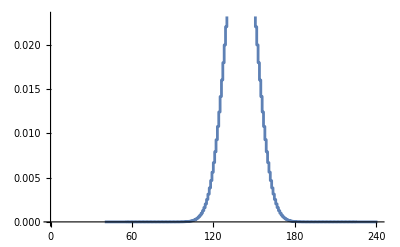

```mathematica
exactDice[sides_]:=∑_(n=1)^Abs[sides] 1/Abs[sides] x^(Sign[sides]*n)
diceList=Table[6,40];
ndice=Length@diceList;
diceDistribution = Product[exactDice[d],{d, diceList}];
probs = CoefficientList[diceDistribution*x^Abs[Total[diceList]], x];
probs = DeleteCases[probs, 0];
values = Exponent[diceDistribution,x,List];
ListStepPlot[Thread[{values, probs}]]
```

A combination-based method. Create tuples to enumerate each possible roll. Sum. Count.

```mathematica
d6 = Range[6];
d12 = Range[12];
dn[sides_]:=Range[sides];
diceList = Table[dn[20],2];
Times@@(Length/@diceList)
```

400

```mathematica
plotRolls[outcomes_]:=
ListStepPlot[
KeySort[
Counts[outcomes]/Length[outcomes]
],
"Center"
]
```

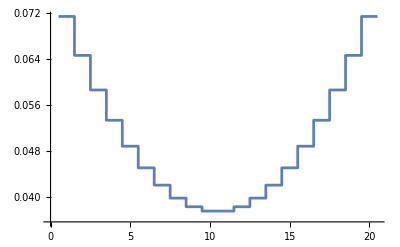

```mathematica
plotRolls[Join[Min/@Tuples[diceList],Max/@Tuples[diceList]]]
```

```mathematica
sortedRoller[list_]:=If[Mod[Median[list],2]==0,Max[list],Min[list]]
summedRoller[list_]:=If[Mod[Total[list],2]==0,Max[list],Min[list]]
```

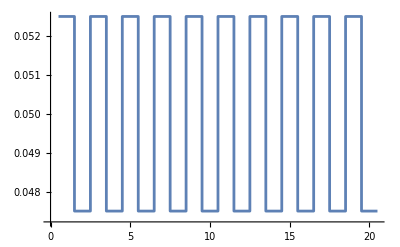

```mathematica
plotRolls[summedRoller/@Tuples[diceList]]
```

```mathematica
Counts[summedRoller/@Tuples[diceList]]
```

<|1→21,3→21,5→21,7→21,9→21,11→21,13→21,15→21,17→21,19→21,2→19,4→19,6→19,8→19,10→19,12→19,14→19,16→19,18→19,20→19|>

```mathematica
Counts[Total[Tuples[diceList],{2}]]
```

<|5→1,6→5,7→15,8→35,9→70,10→126,11→205,12→305,13→420,14→540,15→651,16→735,17→780,18→780,19→735,20→651,21→540,22→420,23→305,24→205,25→126,26→70,27→35,28→15,29→5,30→1|>

```mathematica
Counts[Total[Tuples[diceList],{2}]]/(Times@@(Length/@diceList))
```

<|5→1/7776,6→5/7776,7→5/2592,8→35/7776,9→35/3888,10→7/432,11→205/7776,12→305/7776,13→35/648,14→5/72,15→217/2592,16→245/2592,17→65/648,18→65/648,19→245/2592,20→217/2592,21→5/72,22→35/648,23→305/7776,24→205/7776,25→7/432,26→35/3888,27→35/7776,28→5/2592,29→5/7776,30→1/7776|>

```mathematica
KeySort[%]
```

<|5→1/7776,6→5/7776,7→5/2592,8→35/7776,9→35/3888,10→7/432,11→205/7776,12→305/7776,13→35/648,14→5/72,15→217/2592,16→245/2592,17→65/648,18→65/648,19→245/2592,20→217/2592,21→5/72,22→35/648,23→305/7776,24→205/7776,25→7/432,26→35/3888,27→35/7776,28→5/2592,29→5/7776,30→1/7776|>

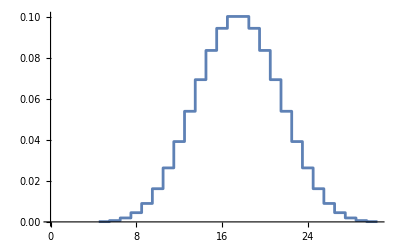

```mathematica
ListStepPlot[%36, Center]
```